```mathematica
Clear["Global`*"]
```

```mathematica
NormalizeMatrixRows[M_]:=Module[{A=M},
For[i=1,i≤Length[M],++i,
A[[i]]=Normalize[M[[i]],Total]
];
Return[A];
]
```

## Model functions

```mathematica
(*Define functions*)
dx[x_,y_]:=r x(1-x/Kx)-y f[x]
dy[x_,y_]:=y(e f[x]-c -w y)
f[x_]:=a x/(1+a h x)

dispersal[i_,k_]:=-d[[i]]Sum[L[[k,l]]x[i,l][t],{l,Nvertices}]
```

## Parameterization

```mathematica
S=2;
(* Spatial web *)
Nvertices=6;
L={{3,-1,-1,0,0,-1},{-1,3,-1,0,-1,0},{-1,-1,2,0,0,0},{0,0,0,1,0,-1},{0,-1,0,0,1,0},{-1,0,0,-1,0,2}};

(* parameters *)
r=2;
Kx=10;

e=1;
c=1;
w=0.2;

a=3;
h=0.5;

X0=1;
Y0=1;

d={1,1};
```

```mathematica
(* Bifurcations *)
(*
	Hopf: a = 2.3 - 2.4
Sattelknoten: Kx=15
*)
```

## Model Equations

```mathematica
(* Homogeneous system equations right hand side *)
rhs[1,k_]:=dx[x[1,k][t],x[2,k][t]]
rhs[2,k_]:=dy[x[1,k][t],x[2,k][t]]
```

```mathematica
Flatten[Table[
x[i,k]'[t]==rhs[i,k],
{i,S},{k,1}]]
```

{x[1,1]'[t]==2 (1-1/10 x[1,1][t]) x[1,1][t]-(3 x[1,1][t] x[2,1][t])/(1+1.5 x[1,1][t]),x[2,1]'[t]==(-1+(3 x[1,1][t])/(1+1.5 x[1,1][t])-0.2 x[2,1][t]) x[2,1][t]}

## Bifurcation Diagram

(-11.7292 | -1.96188
0.00514073 | -0.924839)

(1 | 0
0 | 1)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

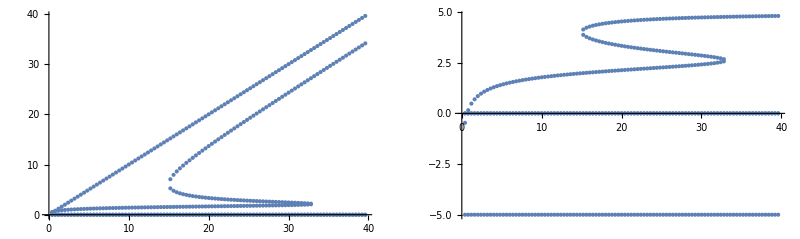

```mathematica
PreyList={};
PredatorList={};
min=0;max=40;
steps=100;
step=(max-min)/steps;
For[i=1,i<steps,++i,
par=min+i*step;
Kx=par;
SteadyStates=Solve[{rhs[1,1]==0,rhs[2,1]==0},{x[1,1][t],x[2,1][t]}];
AppendTo[PreyList,{par,x[1,1][t]}/.SteadyStates];
AppendTo[PredatorList,{par,x[2,1][t]}/.SteadyStates];
];
PreyList=Flatten[PreyList,1];
PredatorList=Flatten[PredatorList,1];
GraphicsRow[{ListPlot[PreyList,PlotRange->All],
ListPlot[PredatorList,PlotRange->All]}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

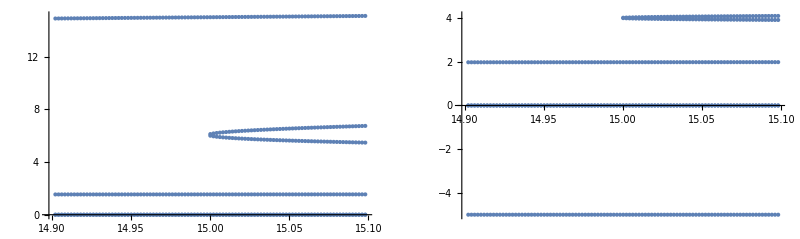

```mathematica
PreyList={};
PredatorList={};
min=14.9;max=15.1;
steps=100;
step=(max-min)/steps;
For[i=1,i<steps,++i,
par=min+i*step;
Kx=par;
SteadyStates=Solve[{rhs[1,1]==0,rhs[2,1]==0},{x[1,1][t],x[2,1][t]}];
AppendTo[PreyList,{par,x[1,1][t]}/.SteadyStates];
AppendTo[PredatorList,{par,x[2,1][t]}/.SteadyStates];
];
PreyList=Flatten[PreyList,1];
PredatorList=Flatten[PredatorList,1];
GraphicsRow[{ListPlot[PreyList,PlotRange->All],
ListPlot[PredatorList,PlotRange->All]}]
```

```mathematica
Kx=14.9;
SteadyStates=Solve[{rhs[1,1]==0,rhs[2,1]==0},{x[1,1][t],x[2,1][t]}]//FullSimplify;
TableForm[SteadyStates]

CalculateJacobian[]:=Module[{},
J=D[
Flatten[Table[rhs[i,k],{i,S},{k,1}]],
{Flatten[Table[x[i,k][t],{i,S},{k,1}]]}
];
J0=FullSimplify[J/.SteadyStates[[5]]];
JM=DiagonalMatrix[Table[d[[i]],{i,S}]];
];

CalculateJacobian[];
kappaList=N[Eigenvalues[L]];
J0//MatrixForm
JM//MatrixForm
Eigenvalues[J0]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

x[1,1][t]→0. | x[2,1][t]→-5.
x[1,1][t]→0. | x[2,1][t]→0.
x[1,1][t]→1.53959 | x[2,1][t]→1.97829
x[1,1][t]→6.01354-0.631177 ⅈ | x[2,1][t]→4.01086-0.0934588 ⅈ
x[1,1][t]→6.01354+0.631177 ⅈ | x[2,1][t]→4.01086+0.0934588 ⅈ
x[1,1][t]→14.9 | x[2,1][t]→0.

(0.268432-0.149915 ⅈ | -1.80217-0.0186918 ⅈ
0.117194-0.0195281 ⅈ | -0.802171-0.0186918 ⅈ)

(1 | 0
0 | 1)

{-0.541241-0.0164359 ⅈ,0.00750188-0.152171 ⅈ}

```mathematica
Kx=15;
SteadyStates=Solve[{rhs[1,1]==0,rhs[2,1]==0},{x[1,1][t],x[2,1][t]}]//FullSimplify;
TableForm[SteadyStates]

CalculateJacobian[]:=Module[{},
J=D[
Flatten[Table[rhs[i,k],{i,S},{k,1}]],
{Flatten[Table[x[i,k][t],{i,S},{k,1}]]}
];
J0=FullSimplify[J/.SteadyStates[[5]]];
JM=DiagonalMatrix[Table[d[[i]],{i,S}]];
];

CalculateJacobian[];
kappaList=N[Eigenvalues[L]];
J0//MatrixForm
JM//MatrixForm
Eigenvalues[J0]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

x[1,1][t]→0. | x[2,1][t]→-5.
x[1,1][t]→0. | x[2,1][t]→0.
x[1,1][t]→1.54205 | x[2,1][t]→1.98165
x[1,1][t]→6. | x[2,1][t]→4.
x[1,1][t]→6.12462 | x[2,1][t]→4.01835
x[1,1][t]→15. | x[2,1][t]→0.

(0.250601 | -1.80367
0.116167 | -0.80367)

(1 | 0
0 | 1)

{-0.537964,-0.0151057}

```mathematica
CalcMaxEigenvalue[]:=Module[{},
Quiet[SteadyStates=Solve[{rhs[1,1]==0,rhs[2,1]==0},{x[1,1][t],x[2,1][t]}]//FullSimplify,Solve::ratnz];

J=D[
Flatten[Table[rhs[i,k],{i,S},{k,1}]],
{Flatten[Table[x[i,k][t],{i,S},{k,1}]]}
];
J0=FullSimplify[J/.SteadyStates[[5]]];
JM=DiagonalMatrix[Table[d[[i]],{i,S}]];

kappaList=N[Eigenvalues[L]];

Return[Max[Re[Eigenvalues[J0]]]];
];
```

```mathematica
list={};
For[Kx=14.99,Kx≤15.01,Kx+=0.001,
AppendTo[list,{Kx,CalcMaxEigenvalue[]}];
];
```

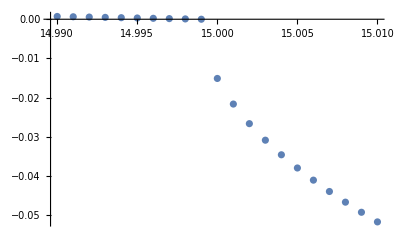

```mathematica
ListPlot[list]
```

```mathematica
(*SetDirectory["/imports/junko.work/brechtel/Early Warning Signs/Saddle Node/export"];Export["SN3-Eigenvalues.CSV",list]*)
```

SN3-Eigenvalues.CSV

```mathematica
CalcMaxEigenvalue[]:=Module[{},
Quiet[SteadyStates=Solve[{rhs[1,1]==0,rhs[2,1]==0},{x[1,1][t],x[2,1][t]}]//FullSimplify,Solve::ratnz];

J=D[
Flatten[Table[rhs[i,k],{i,S},{k,1}]],
{Flatten[Table[x[i,k][t],{i,S},{k,1}]]}
];
J0=FullSimplify[J/.SteadyStates[[5]]];
JM=DiagonalMatrix[Table[d[[i]],{i,S}]];

kappaList=N[Eigenvalues[L]];

Return[Re[Table[Eigenvalues[J0-kappa JM],{kappa,kappaList}]]];
];
```

```mathematica
list={};
For[Kx=14.5,Kx≤15.5,Kx+=0.01,
AppendTo[list,Flatten[{Kx,CalcMaxEigenvalue[]}]];
];
```

```mathematica
ListPlot[list]
```

-Graphics-

```mathematica
SetDirectory["/imports/junko.work/brechtel/Early Warning Signs/Sorted Models/Saddle Node/export"];Export["SN-Eigenvalues-all.CSV",list]
```

SN-Eigenvalues-all.CSV

```mathematica
list[[1]]
```

{14.5,-4.94887,-4.35883,-4.25386,-3.66382,-2.91558,-2.32554,-1.69305,-1.103,-0.969207,-0.379164,-0.556113,0.0339299}

## Homogen System

```mathematica
(*set starting conditions*)
setStartHomogen[]:=Module[{delta=0.01},
startHomogen=
Flatten[
Table[
{x[1,k][0]==X0,
x[2,k][0]==Y0},
{k,1}]
];
];

(*Solve ODE*)
solveHomogen[Tmax_]:=Module[{sol},
setStartHomogen[];
sol=NDSolve[Join[{eqnsHomogen,startHomogen}],varsHomogen,{t,0,Tmax},MaxSteps->100000][[1]];
Return[varsHomogen/.sol];
];

EvaluateHomogenSystem[Tmax_]:=Module[{},
(*generate equations*)
eqnsHomogen=Flatten[Table[
x[i,k]'[t]==rhs[i,k],
{i,S},{k,1}]];

(*dependent variables*)
varsHomogen = Flatten[
Table[
x[i,k][t]
,{i,S},{k,1}]
];

(*solve deqns*)
solHomogen=solveHomogen[Tmax];
XSList=solHomogen/.t->Tmax;

(*set steady state values*)
For[i=1,i≤S,++i,
XS[i]=XSList[[i]];
(*TS[i]=Sum[c[[i,j]]XS[j],{j,S}];*)
];
];
```

## Solver

### Local

```mathematica
(* Euler-Verfahren *)
(* ohne Noise *)
EulerLocal[]:=Module[{y},
Tmax=100.;
maxsteps=100000;
dt=Tmax/maxsteps;

data=Table[0,{maxsteps},{i,S}];
eqns=Flatten[Table[rhs[i,k],{i,S},{k,1}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,1}]];

data[[1,1]]=X0;
data[[1,2]]=Y0;

For[step=1,step<maxsteps,step++,
k=1;
For[i=1,i≤S,++i,
y[i,k]=data[[step,i]];
];
data[[step+1]]=data[[step]]+eqns dt;
];
];
```

```mathematica
(* Euler-Maruyama-Verfahren *)
(* Wiener Prozess *)
EulerMaruyamaLocal[noise_,tmax_,maxSteps_]:=Module[{y},
Tmax=tmax;
maxsteps=maxSteps;
dt=Tmax/maxsteps;
Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S}];
data=Table[0,{maxsteps},{i,S}];
eqns=Flatten[Table[rhs[i,k],{i,S},{k,1}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,1}]];

data[[1,1]]=X0;
data[[1,2]]=Y0;

For[step=1,step<maxsteps,step++,
k=1;
For[i=1,i≤S,++i,
y[i,k]=data[[step,i]];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
];
];

EulerMaruyamaLocal[noise_]:=Module[{y},
EulerMaruyamaLocal[noise,100,100000];
];
```

### Spatial

```mathematica
(* Euler-Verfahren *)
(* ohne Noise *)
EulerSpatial[Tmax_,maxsteps_]:=Module[{y},
dt=Tmax/maxsteps;

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+dispersal[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

For[k=1,k≤Nvertices,++k,
data[[1,1,k]]=X0;
data[[1,2,k]]=Y0;
];

For[step=1,step<maxsteps,step++,
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt;
];
];
```

```mathematica
(* Euler-Maruyama-Verfahren *)
(* Wiener Prozess *)
EulerMaruyamaSpatial[noise_,Tmax_,maxsteps_]:=Module[{y},
dt=Tmax/maxsteps;

(*noise=0.01;*)
Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+dispersal[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

For[k=1,k≤Nvertices,++k,
data[[1,1,k]]=X0;
data[[1,2,k]]=Y0;
];

For[step=1,step<maxsteps,step++,
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
];
];
```

```mathematica
EulerMaruyamaSpatial[noise_,Tmax_,maxsteps_,initialData_]:=Module[{y},
dt=Tmax/maxsteps;

(*noise=0.01;*)
Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+dispersal[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

data[[1]]=initialData;

For[step=1,step<maxsteps,step++,
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
];
];
```

```mathematica
EulerMaruyamaSpatialFixedRoot[noise_,Tmax_,maxsteps_]:=Module[{y, factor},
dt=Tmax/maxsteps;

SteadyState=Solve[{rhs[1,1]==0,rhs[2,1]==0},{x[1,1][t],x[2,1][t]}][[5]][[All,2]]//Re;
factor=noise*Table[Sqrt[SteadyState[[i]]],{i,S},{k,Nvertices}];
Print[factor];

(*noise=0.01;*)
Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+dispersal[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

For[k=1,k≤Nvertices,++k,
data[[1,1,k]]=X0;
data[[1,2,k]]=Y0;
];

For[step=1,step<maxsteps,step++,
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt+factor Noise[];
];
];
```

```mathematica
EulerMaruyamaSpatialFixedRoot[noise_,Tmax_,maxsteps_,initialData_]:=Module[{y,factor},
dt=Tmax/maxsteps;

SteadyState=Solve[{rhs[1,1]==0,rhs[2,1]==0},{x[1,1][t],x[2,1][t]}][[5]][[All,2]]//Re;
factor=noise*Table[Sqrt[SteadyState[[i]]],{i,S},{k,Nvertices}];

(*noise=0.01;*)
Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+dispersal[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

data[[1]]=initialData;

For[step=1,step<maxsteps,step++,
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt+factor Noise[];
];
];
```

### Local variable Kx

```mathematica
(* Euler-Verfahren *)
(* ohne Noise *)
EulerLocalVariable[KxInterval_]:=Module[{y,Kxstep,Kxt,step},
Tmax=100.;
maxsteps=100000;
dt=Tmax/maxsteps;

Kxstep=(KxInterval[[2]]-KxInterval[[1]])/maxsteps;
Kx=Kxt;

data=Table[0,{maxsteps},{i,S}];
eqns=Flatten[Table[rhs[i,k],{i,S},{k,1}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,1}]];

data[[1,1]]=X0;
data[[1,2]]=Y0;

For[step=1,step<maxsteps,step++,
Kxt=KxInterval[[1]]+step Kxstep;
k=1;
For[i=1,i≤S,++i,
y[i,k]=data[[step,i]];
];
data[[step+1]]=data[[step]]+eqns dt;
];
];
```

```mathematica
(* Euler-Maruyama-Verfahren *)
(* Wiener Prozess *)
EulerMaruyamaLocalVariable[KxInterval_,noise_,tmax_,maxSteps_]:=Module[{y,Kxstep,Kxt,step},
Tmax=tmax;
maxsteps=maxSteps;
dt=Tmax/maxsteps;

Kxstep=(KxInterval[[2]]-KxInterval[[1]])/maxsteps;
Kx=Kxt;

Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S}];
data=Table[0,{maxsteps},{i,S}];
eqns=Flatten[Table[rhs[i,k],{i,S},{k,1}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,1}]];

data[[1,1]]=X0;
data[[1,2]]=Y0;

For[step=1,step<maxsteps,step++,
Kxt=KxInterval[[1]]+step Kxstep;
k=1;
For[i=1,i≤S,++i,
y[i,k]=data[[step,i]];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
];
];

EulerMaruyamaLocalVariable[KxInterval_,noise_]:=Module[{y},
EulerMaruyamaLocalVariable[KxInterval,noise,100,100000];
];
```

### Spatial variable Kx

```mathematica
(* Euler-Verfahren *)
(* ohne Noise *)
EulerSpatialVariable[KxInterval_]:=Module[{y,Kxstep,Kxt,step},
Tmax=500.;
maxsteps=100000;
dt=Tmax/maxsteps;

Kxstep=(KxInterval[[2]]-KxInterval[[1]])/maxsteps;
Kx=Kxt;

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+dispersal[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
data[[1,1,k]]=X0;
data[[1,2,k]]=Y0;
];
];

For[step=1,step<maxsteps,step++,
Kxt=KxInterval[[1]]+step Kxstep;
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt;
];
];
```

```mathematica
(* Euler-Maruyama-Verfahren *)
(* Wiener Prozess *)
EulerMaruyamaSpatialVariable[KxInterval_,noise_,tmax_,maxSteps_]:=Module[{y,Kxstep,Kxt},
Tmax=tmax;
maxsteps=maxSteps;
dt=Tmax/maxsteps;

Kxstep=(KxInterval[[2]]-KxInterval[[1]])/maxsteps;
Kx=Kxt;

Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+dispersal[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

For[k=1,k≤Nvertices,++k,
data[[1,1,k]]=X0;
data[[1,2,k]]=Y0;
];

For[step=1,step<maxsteps,step++,
Kxt=KxInterval[[1]]+step Kxstep;
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
];
];

EulerMaruyamaSpatialVariable[KxInterval_,noise_]:=Module[{y},
EulerMaruyamaSpatialVariable[KxInterval,noise,100,100000];
];

EulerMaruyamaSpatialVariable[KxInterval_,noise_,tmax_,maxSteps_,initialData_]:=Module[{y,Kxt,Kxstep},
Tmax=tmax;
maxsteps=maxSteps;
dt=Tmax/maxsteps;

Kxstep=(KxInterval[[2]]-KxInterval[[1]])/maxsteps;
Kx=Kxt;

Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+dispersal[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

data[[1]]=initialData;

For[step=1,step<maxsteps,step++,
Kxt=KxInterval[[1]]+step Kxstep;
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
];
];
```